```mathematica
SetDirectory[NotebookDirectory[]<>"\\MethodsODE\\OutputData\\"]
```

D:\BMSTU\3 COURSE\6th term\Numeric Methods\Lab1\methodsODE\MethodsODE\OutputData

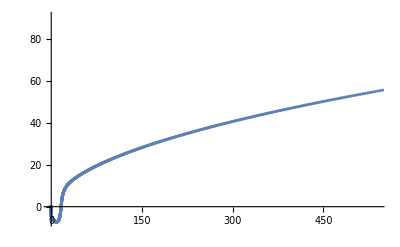

```mathematica
data1 = Import["eulerImplicit-1", "Table"];
pl1=ListPlot[Table[data1[[i]],{i,2, Length[data1],2}]]
```

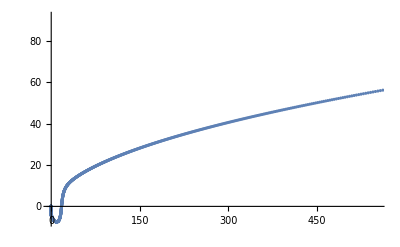

```mathematica
data2 = Import["eulersimple-1", "Table"];
pl3=ListPlot[Table[data2[[i]],{i,2, Length[data2],2}]]
```

```mathematica
sol1 = Expand@NDSolve[{x'[t]==2x[t]+(y[t])^2-1, y'[t]==6x[t]-(y[t])^2+1, x[0]==0,y[0]==0},{x[t],y[t]},{t,0,2}];
```

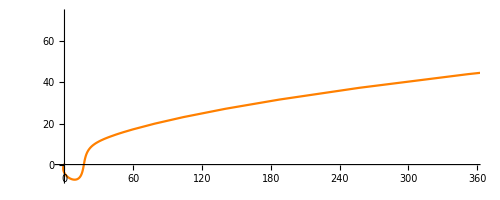

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

```mathematica
pl2=ParametricPlot[{x[t],y[t]}/.sol1, {t,0,2},PlotStyle->Orange]
```

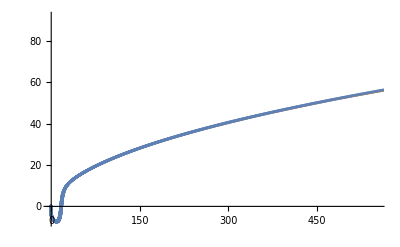

```mathematica
Show[pl3,pl2,pl1]
```